Bessel

```mathematica
$Assumptions={τ>0,τR>0,t>=0,τ-t>=0};
```

```mathematica
Psi[t_]=BesselJ[0,t/τR];
dPsi[t_]=D[Psi[t],t];
ddPsi[t_]=D[dPsi[t],t];
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi[t],t,s]);

c0=SeriesCoefficient[f[s],{s,0,0}];
```

```mathematica
Clear[τR];

g[t_]=(t+τR)/(τ+2τR);

gs[t_]=c0(DiracDelta[t]-DiracDelta[τ-t])/(τ+2τR);


h1[t_]=t/τ;
h2[t_]=t/τ+Sin[ π t/τ];
```

```mathematica
Wh1[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]h1[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h1[t]h1[u],{t,0,τ},{u,0,τ}]
```

-1/2+BesselJ[0,τ/τR]+1/2 (1-Hypergeometric0F1Regularized[2,-τ^2/(4 τR^2)])+(τ^2 HypergeometricPFQ[{3/2},{2,5/2},-τ^2/(4 τR^2)])/(6 τR^2)

```mathematica
data=List[];

τR=1;

data=Table[{τ,Psi[0]/2+NIntegrate[dPsi[τ-t]h2[t],{t,0,τ}]-1/2 NIntegrate[ddPsi[t-u]h2[t]h2[u],{t,0,τ},{u,0,τ}]},{τ,0.001,0.01-0.001/5,0.001/5}];

Do[

aux=Table[{τ,Psi[0]/2+NIntegrate[dPsi[τ-t]h2[t],{t,0,τ}]-1/2 NIntegrate[ddPsi[t-u]h2[t]h2[u],{t,0,τ},{u,0,τ},Method->"LocalAdaptive"]},{τ,0.001*10^n+0.002*10^(n-1),0.001*10^(n+1),0.002*10^(n-1)}];

Do[

data=AppendTo[data,aux[[j]]];

,{j,1,45}];

,{n,1,4}];

Clear[τR]
```

```mathematica
W0[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]g[t]g[u],{t,0,τ},{u,0,τ}];
```

```mathematica
W1[τ_]=W0[τ]+c0 dPsi[τ]/(τ+2τR)-c0/(τ+2τR)Integrate[ddPsi[t]g[t],{t,0,τ}]+c0/(τ+2τR)Integrate[ddPsi[τ-t]g[t],{t,0,τ}]-c0^2/(τ+2τR)^2 ddPsi[0]+c0^2/(τ+2τR)^2 ddPsi[τ];
```

```mathematica
Wh1[τ_]=-1/2+BesselJ[0,τ/τR]+1/2 (1-Hypergeometric0F1Regularized[2,-τ^2/(4 τR^2)])+(τ^2 HypergeometricPFQ[{3/2},{2,5/2},-τ^2/(4 τR^2)])/(6 τR^2);
```

```mathematica
data={{0.001,0.5000000804878473},{0.0012000000000000001,0.5000001159024982},{0.0014,0.5000001577561749},{0.0016,0.5000002060488768},{0.0018,0.5000002607806029},{0.002,0.5000003219513522},{0.0022,0.5000003895611237},{0.0024000000000000002,0.500000463609916},{0.0026,0.5000005440977279},{0.0028000000000000004,0.5000006310245577},{0.003,0.5000007243904041},{0.0032,0.5000008241952651},{0.0034000000000000002,0.5000009304391391},{0.0036000000000000003,0.5000010431220239},{0.0038,0.5000011622439177},{0.004,0.500001287804818},{0.004200000000000001,0.5000014198047229},{0.0044,0.5000015582436297},{0.0046,0.5000017031215358},{0.0048000000000000004,0.5000018544384388},{0.005,0.5000020121943357},{0.005200000000000001,0.5000021763892237},{0.0054,0.5000023470230998},{0.0056,0.5000025240959608},{0.0058000000000000005,0.5000027076078035},{0.006,0.5000028975586246},{0.006200000000000001,0.5000030939484205},{0.0064,0.5000032967771875},{0.0066,0.5000035060449222},{0.0068000000000000005,0.5000037217516204},{0.007,0.5000039438972783},{0.007200000000000001,0.500004172481892},{0.0074,0.5000044075054569},{0.0076,0.5000046489679691},{0.0078000000000000005,0.500004896869424},{0.008,0.5000051512098169},{0.0082,0.5000054119891434},{0.008400000000000001,0.5000056792073985},{0.0086,0.5000059528645774},{0.0088,0.500006232960675},{0.009000000000000001,0.5000065194956863},{0.0092,0.5000068124696059},{0.009400000000000002,0.5000071118824285},{0.009600000000000001,0.5000074177341486},{0.0098,0.5000077300247605},{0.012,0.5000115901866439},{0.014,0.500015775500451},{0.016,0.5000206046880065},{0.018000000000000002,0.5000260777404462},{0.02,0.5000321946477241},{0.022,0.5000389553986123},{0.024,0.5000463599807012},{0.026000000000000002,0.5000544083803994},{0.028,0.5000631005829336},{0.030000000000000002,0.5000724365723488},{0.032,0.5000824163315085},{0.034,0.5000930398420947},{0.036000000000000004,0.5001043070846074},{0.038000000000000006,0.5001162180383653},{0.04,0.5001287726815054},{0.041999999999999996,0.5001419709909833},{0.044,0.5001558129425734},{0.046,0.5001702985108685},{0.048,0.50018542766928},{0.05,0.5002012003900382},{0.052000000000000005,0.5002176166441923},{0.054000000000000006,0.5002346764016099},{0.055999999999999994,0.5002523796309781},{0.057999999999999996,0.5002707262998026},{0.06,0.5002897163744082},{0.062,0.500309349819939},{0.064,0.500329626600358},{0.066,0.5003505466784477},{0.068,0.5003721100158101},{0.07,0.500394316572866},{0.072,0.5004171663088565},{0.074,0.5004406591818418},{0.076,0.5004647951487019},{0.078,0.5004895741651365},{0.08,0.5005149961856653},{0.082,0.5005410611636281},{0.084,0.5005677690511844},{0.086,0.500595119799314},{0.088,0.5006231133578171},{0.09,0.5006517496753141},{0.092,0.500681028699246},{0.094,0.5007109503758743},{0.096,0.5007415146502812},{0.098,0.5007727214663699},{0.09999999999999999,0.5008045707668641},{0.12000000000000001,0.5011583869706056},{0.14,0.5015763798616348},{0.16,0.5020584727304381},{0.18,0.5026045771093056},{0.2,0.5032145927908547},{0.22000000000000003,0.5038884078490099},{0.24,0.5046258986624346},{0.26,0.5054269299404083},{0.28,0.5062913547511446},{0.3,0.5072190145525425},{0.32,0.5082097392253626},{0.34,0.5092633471088232},{0.36,0.510379645038605},{0.38,0.5115584283872572},{0.4,0.5127994811069952},{0.42,0.5141025757748793},{0.44,0.5154674736403635},{0.46,0.5168939246752051},{0.48,0.5183816676257209},{0.5,0.5199304300673792},{0.52,0.5215399284617138},{0.54,0.5232098682155486},{0.56,0.5249399437425152},{0.5800000000000001,0.5267298385191482},{0.6,0.5285792251716672},{0.62,0.5304877655562836},{0.64,0.5324551107287154},{0.66,0.5344809011565151},{0.68,0.5365647667126987},{0.7,0.5387063267707044},{0.72,0.5409051902837081},{0.74,0.5431609558660833},{0.76,0.5454732118618877},{0.78,0.5478415364706875},{0.8,0.5502654978232309},{0.8200000000000001,0.5527446540177025},{0.84,0.555278553244249},{0.86,0.5578667339632898},{0.88,0.5605087249284687},{0.9,0.5632040450750905},{0.92,0.5659522040522149},{0.9400000000000001,0.5687527020243597},{0.96,0.5716050298491273},{0.98,0.5745086691512495},{1.,0.5774630925130086},{1.2,0.6096781361739096},{1.4,0.6463283143143396},{1.6,0.6867548693190427},{1.8,0.7302360951622642},{2.,0.7760020103885299},{2.2,0.8232498775928907},{2.4000000000000004,0.8711602161356022},{2.6,0.9189129343576512},{2.8,0.9657032340941818},{3.,1.0107569268193954},{3.2,1.0533448315549894},{3.4000000000000004,1.0927959476319988},{3.6000000000000005,1.128509129578614},{3.8,1.1599630306788995},{4.,1.1867241480771256},{4.2,1.2084526902589234},{4.4,1.2249066541571383},{4.6000000000000005,1.2359431357386708},{4.8,1.2415180786583513},{5.,1.2416835697797146},{5.2,1.236583288542081},{5.4,1.2264461296357085},{5.6000000000000005,1.2115782261954278},{5.800000000000001,1.1923535858456138},{6.000000000000001,1.1692036402873331},{6.2,1.1426059552029437},{6.4,1.1130723852541193},{6.6000000000000005,1.0811370387787922},{6.800000000000001,1.0473442358376528},{7.000000000000001,1.0122368321354707},{7.2,0.9763451388132265},{7.4,0.9401766620863183},{7.6000000000000005,0.9042068798450298},{7.800000000000001,0.8688712583124878},{8.,0.8345586173910966},{8.2,0.8016058945487885},{8.4,0.7702945218487935},{8.6,0.740848207405175},{8.8,0.7134322952676428},{9.,0.6881545317458839},{9.2,0.6650671759757594},{9.4,0.6441703337153022},{9.6,0.6254163064203846},{9.799999999999999,0.6087149111744572},{10.,0.5939394523600658},{12.,0.511335339612345},{14.,0.4421791243935025},{16.,0.37074589709569494},{18.,0.3332812010522719},{20.,0.3038057648681243},{22.,0.2698920295079299},{24.,0.24806788817268854},{26.,0.23177520400815532},{28.,0.21228460072426103},{30.,0.19782695401811679},{32.,0.18742208560090878},{34.,0.17497077918375337},{36.,0.16463344212559017},{38.,0.1573280433894444},{40.,0.14881192467031745},{42.,0.14104300059735442},{44.,0.13555491105768835},{46.,0.12944544149154136},{48.,0.12341575740910593},{50.,0.1190847838921707},{52.,0.11453530024483527},{54.,0.10973296289310652},{56.,0.10619000533346701},{58.,0.10266974793297567},{60.,0.09878600873895338},{62.,0.09581760283740048},{64.,0.09302115239222353},{66.,0.0898609995270998},{68.,0.0872913603988037},{70.,0.08502985181516531},{72.,0.08241476642126155},{74.,0.0801728074469199},{76.,0.07828442118816215},{78.,0.07609446560411115},{80.,0.07413443667789843},{82.,0.07251439698602113},{84.,0.0706721760883573},{86.,0.06905350815426092},{88.,0.06701623419313485},{90.,0.06604633292678153},{92.,0.06443829881528318},{94.,0.06318032459163736},{96.,0.06175022104868422},{98.,0.060590968906188536},{100.,0.059387082686697346}};

Wh2=Interpolation[data];
```

```mathematica
W0[τ_]=1/2+(τ^2+2 τ τR+2 τR^2-2 τR (τ+τR) BesselJ[0,τ/τR]-2 τ τR BesselJ[1,τ/τR])/(2 (τ+2 τR)^2)+(6 τR^2 (τ+τR) (-1+BesselJ[0,τ/τR])+τ^3 HypergeometricPFQ[{3/2},{2,5/2},-τ^2/(4 τR^2)])/(6 τR^2 (τ+2 τR));
```

```mathematica
W1[τ_]=1/2+τR^2/(2 (τ+2 τR)^2)+(τR^2 (-1+BesselJ[0,τ/τR]-BesselJ[1,τ/τR]))/(τ+2 τR)^2-(τR BesselJ[1,τ/τR])/(τ+2 τR)+(τ^2+2 τ τR+2 τR^2-2 τR (τ+τR) BesselJ[0,τ/τR]-2 τ τR BesselJ[1,τ/τR])/(2 (τ+2 τR)^2)+(τR (τR (-1+BesselJ[0,τ/τR])+(τ+τR) BesselJ[1,τ/τR]))/(τ+2 τR)^2-(τR^2 (BesselJ[0,τ/τR]-BesselJ[2,τ/τR]))/(2 (τ+2 τR)^2)+(6 τR^2 (τ+τR) (-1+BesselJ[0,τ/τR])+τ^3 HypergeometricPFQ[{3/2},{2,5/2},-τ^2/(4 τR^2)])/(6 τR^2 (τ+2 τR));
```

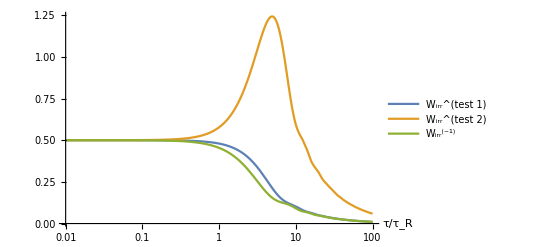

```mathematica
τR=1;
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test 1)"],Legended[Wh2[τ],"W_irr^(test 2)"],Legended[W0[τ],"W_irr^(-1)"]},{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR]
```

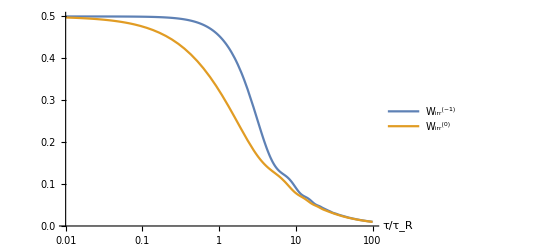

```mathematica
τR=1;
LogLinearPlot[{Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR]
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

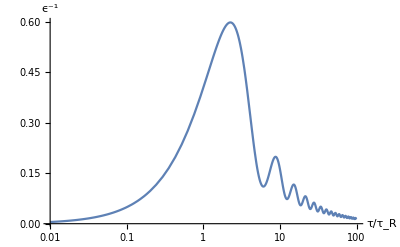

```mathematica
τR=1;
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^-1"}]
Clear[τR]
```

```mathematica
τR=1;

data=Table[{τ,ϵ1[τ]},{τ,0.001,0.01,0.001/100}];

Do[

aux=Table[{τ,ϵ1[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data=AppendTo[data,aux[[j]]];

,{j,1,91}];

,{n,1,4}];

Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi4.dat",data];

Clear[τR]
```